## Official lattice

S-band longitudinal wakes from official MAD8 lattice: https://www.slac.stanford.edu/cgi-bin/cvsweb/optics/etc/lattice/facet2/sband_l.dat?cvsroot=LCLS

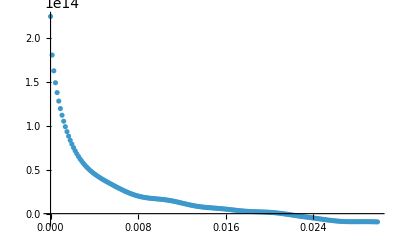

```mathematica
raw = Import["~/Downloads/sband_l.dat"];
raw=raw[[2;;]];

ListPlot[raw[[All,{2,3}]],PlotRange->All]
```

-Graphics-

## Bmad

(base) nmajik@dhcp-visitor-216-95 wakefields % cat longitudinal_wakes_sband.bmad 
! Adapted from file: 	elegant/Sz_p5um_10mm_per35mm_cell.sdds
! Usage: 
! ele[sr_wake] = call::longitudinal_wakes_sband.bmad

{
  scale_with_length = T, 
  longitudinal = {1.0214527206425931e14, 200.737972823806, 0, 0.25, none},
  longitudinal = {2.0264683145205535e13, 164752.58575866005, 0, 0.25, none},
  longitudinal = {9.111515497722739e13, 1206.8246815698092, 0, 0.25, none},
  longitudinal = {4.95817609185586e13, 9050.772842025624, 0, 0.25, none},
z_max = 0.01}

```mathematica
wakeSpecs = {
{1.02*^14, 200.737972823806},
{2.02*^13,164752.58575866005},
{9.11*^13,1206.8246815698092},
{4.96*^13,9050.772842025624}
};
```

-Graphics-

So it appears that the data file has no frequency terms! Is it just building up the wake from exponentials?

```mathematica
wakeExprs = #[[1]]*Exp[-#[[2]]*z]&/@wakeSpecs;
```

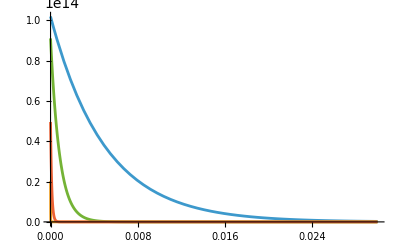

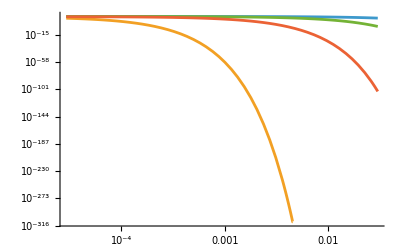

```mathematica
Plot[
wakeExprs,{z,0,0.03},
PlotRange->All
]
LogLogPlot[
wakeExprs,{z,0,0.03},
PlotRange->All
]
```

```mathematica
wakeSumExpr = Total[wakeExprs];
```

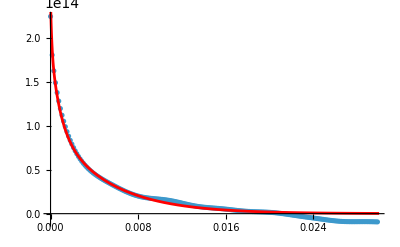

```mathematica
Show[
ListPlot[raw[[All,{2,3}]],PlotRange->All],
Plot[
wakeSumExpr,{z,0,0.03},
PlotRange->All,
PlotStyle->Red
]
]
```

Not bad! And the Bmad file specifies z_max = 0.01 and the agreement really is quite good up to that point

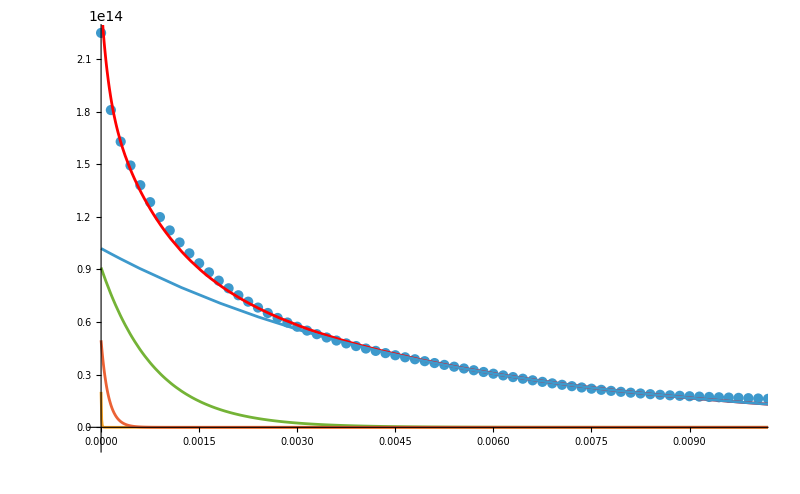

```mathematica
Show[
ListPlot[raw[[All,{2,3}]],PlotRange->{{0,0.01},All},ImageSize->800],
Plot[
wakeSumExpr ,{z,0,0.03},
PlotRange->All,
PlotStyle->Red
],
Plot[
wakeExprs,{z,0,0.03},
PlotRange->All
]
]
```

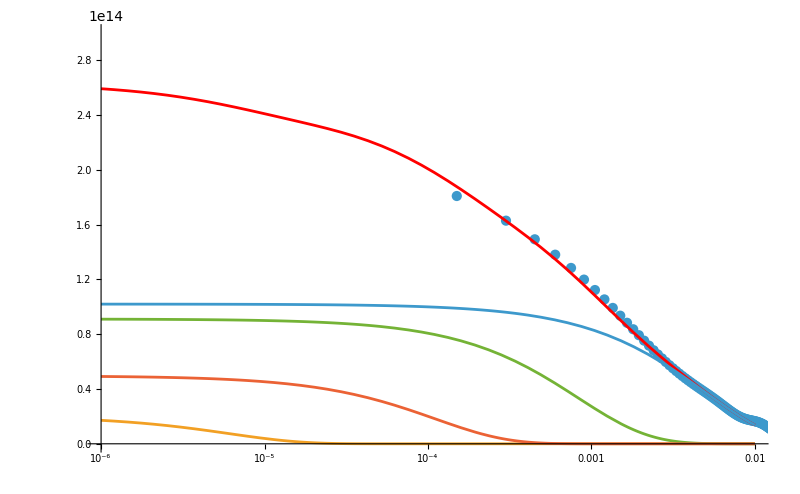

```mathematica
Show[
ListLogLinearPlot[raw[[All,{2,3}]],PlotRange->{{1*^-6,0.01},{0,3*^14}},ImageSize->800],
LogLinearPlot[
wakeSumExpr ,{z,1*^-6,0.01},
PlotRange->All,
PlotStyle->Red
],
LogLinearPlot[
wakeExprs,{z,1*^-6,0.01},
PlotRange->All
]
]
```

# Self-smart the pseudomodes

```mathematica
raw = Import["~/Downloads/sband_l.dat"];
raw=raw[[2;;]];
```

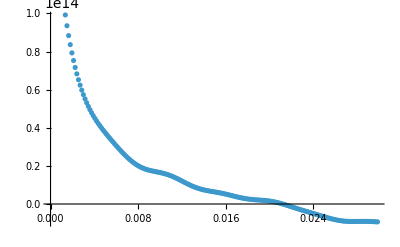

```mathematica
ListPlot[raw[[All,{2,3}]]]
```

```mathematica
fitData = Select[raw[[All,{2,3}]] ,#[[1]]<0.01&];
```

```mathematica
n=4;
expr = Sum[Subscript[a, i] * Exp[- Subscript[b, i] z],{i,1,n}]
coeffs = Flatten[
Table[{
{Subscript[a, i],i*10^13},
{Subscript[b, i],i*100}
},{i,1,n}],1]

nlm=NonlinearModelFit[
fitData,
expr,
coeffs,
z,
Method->{"NMinimize",Method->"DifferentialEvolution"},
MaxIterations->1000
]
```

ⅇ^(-z b_1) a_1+ⅇ^(-z b_2) a_2+ⅇ^(-z b_3) a_3+ⅇ^(-z b_4) a_4

{{a_1,10000000000000},{b_1,100},{a_2,20000000000000},{b_2,200},{a_3,30000000000000},{b_3,300},{a_4,40000000000000},{b_4,400}}

FittedModel[…]

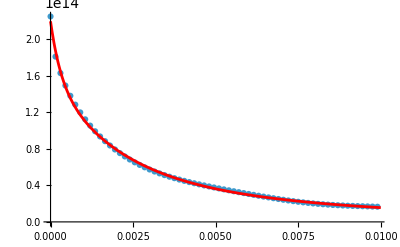

```mathematica
Show[
ListPlot[fitData],
Plot[nlm["BestFit"],{z,0,0.01},PlotStyle->{Red}]
]
```

```mathematica
nlm["BestFit"]
```

6.04711×10^13 ⅇ^(-3232.88 z)+9.48788×10^13 ⅇ^(-545.898 z)+5.32743×10^13 ⅇ^(-180.224 z)+1.09719×10^13 ⅇ^(-53.8656 z)

```mathematica
nlm["BestFitParameters"]
```

{a_1→1.09719×10^13,b_1→53.8656,a_2→9.48788×10^13,b_2→545.898,a_3→5.32743×10^13,b_3→180.224,a_4→6.04711×10^13,b_4→3232.88}

```mathematica
NotebookDirectory[]
```

/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/ARCHIVE/

# Transverse

# Self-smart the pseudomodes

```mathematica
raw = Import["~/Downloads/sband_t.dat"];
raw=raw[[2;;]];
```

```mathematica
ListPlot[raw[[All,{2,3}]]]
```

-Graphics-

```mathematica
raw[[1;;5]]
```

{{1,0.,0.},{2,0.00015,3.71163×10^14},{3,0.0003,6.94799×10^14},{4,0.00045,9.87025×10^14},{5,0.0006,1.25342×10^15}}

### n = 4

I think our bunches tend to be very, very short compared to this data range which extends to 3 cm
In contrast our bunches are, at most, a few hundred microns long throughout L2 and L3

As such, I think it’s really important to focus on this region and, especially, ensure that the function goes very close to zero at ζ = 0

```mathematica
(*fitData = Select[raw[[All,{2,3}]] ,#[[1]]<0.01&];*) (*Limit fitting range*)
zMax = 0.005;
fitData = Select[raw[[All,{2,3}]] ,#[[1]]<zMax&];
```

```mathematica
n=4;
expr = Sum[Subscript[a, i] * Exp[- Subscript[b, i] z],{i,1,n}]
coeffs = Flatten[
Table[{
{Subscript[a, i],RandomReal[{-1*^16,1*^16}]},
{Subscript[b, i],RandomReal[{0,2000}]}
},{i,1,n}],1];

nlm=NonlinearModelFit[
fitData,
expr,
coeffs,
z,
(*Method->{"NMinimize",(*Method->"NelderMead"*)Method->"DifferentialEvolution"},*)
MaxIterations->5000
]

nlm["BestFitParameters"]
```

ⅇ^(-z b_1) a_1+ⅇ^(-z b_2) a_2+ⅇ^(-z b_3) a_3+ⅇ^(-z b_4) a_4

FittedModel[…]

{a_1→-1.64568×10^15,b_1→729.479,a_2→-1.70707×10^15,b_2→729.479,a_3→5.30637×10^15,b_3→-40.0701,a_4→-1.95954×10^15,b_4→-40.0701}

```mathematica
Show[
ListPlot[fitData,PlotRange->{{0,0.03},Automatic}],
Plot[nlm["BestFit"],{z,0,0.03},PlotStyle->{Red}]
]
```

-Graphics-

```mathematica
Show[
ListPlot[fitData,PlotRange->{{0,zMax},Automatic}],
Plot[nlm["BestFit"],{z,0,zMax},PlotStyle->{Red}]
]
```

-Graphics-

```mathematica
nlm["BestFit"]
```

-1.70707×10^15 ⅇ^(-729.479 z)-1.64568×10^15 ⅇ^(-729.479 z)-1.95954×10^15 ⅇ^(40.0701 z)+5.30637×10^15 ⅇ^(40.0701 z)

```mathematica
nlm4=nlm;
```

```mathematica
nlm4[0]
```

-5.91272×10^12

```mathematica
nlm4[10*^-6]
```

1.97972×10^13

### Specialized constraints

Assert the sum of a_i = 0
Instead of doing it as a constraint on the optimizer, build it directly into the fit expression

```mathematica
(*fitData = Select[raw[[All,{2,3}]] ,#[[1]]<0.01&];*) (*Limit fitting range*)
zMax = 0.005;
fitData = Select[raw[[All,{2,3}]] ,#[[1]]<zMax&];
```

```mathematica
n=2;
expr = Sum[Subscript[a, i] * Exp[- Subscript[b, i] z],{i,1,n}]
coeffs =
Table[
{Subscript[a, i],RandomReal[{-1*^16,1*^16}]},
{i,1,n-1}
]~Join~
Table[
{Subscript[b, i],RandomReal[{0,2000}]},
{i,1,n}];

coeffs =
Table[
{Subscript[a, i],1*^15},
{i,1,n-1}
]~Join~
Table[
{Subscript[b, i],1},
{i,1,n}];

(*Apply specialized constraint*)
expr = expr/.Subscript[a, n]->(-Sum[Subscript[a, i],{i,n-1}])


nlm=NonlinearModelFit[
fitData,
expr,
coeffs,
z,
(*Method->{"NMinimize",(*Method->"NelderMead"*)Method->"DifferentialEvolution"},*)

MaxIterations->5000
]

nlm["BestFitParameters"]
```

ⅇ^(-z b_1) a_1+ⅇ^(-z b_2) a_2

ⅇ^(-z b_1) a_1-ⅇ^(-z b_2) a_1

FittedModel[…]

{a_1→3.36123×10^15,b_1→-39.2988,b_2→724.095}

```mathematica
Show[
ListPlot[fitData,PlotRange->{{0,0.03},Automatic}],
Plot[nlm["BestFit"],{z,0,0.03},PlotStyle->{Red}]
]
```

-Graphics-

```mathematica
Show[
ListPlot[fitData,PlotRange->{{0,zMax},Automatic}],
Plot[nlm["BestFit"],{z,0,zMax},PlotStyle->{Red}]
]
```

-Graphics-

```mathematica
nlm["BestFit"]
```

-3.36123×10^15 ⅇ^(-724.095 z)+3.36123×10^15 ⅇ^(39.2988 z)

```mathematica
nlm4=nlm;
```

```mathematica
nlm4[0]
```

0.

```mathematica
nlm4[10*^-6]
```

2.55718×10^13

### n = 8

```mathematica
(*fitData = Select[raw[[All,{2,3}]] ,#[[1]]<0.01&];*)
fitData = raw[[All,{2,3}]]; (*Fit whole range*)
```

```mathematica
n=8;
expr = Sum[Subscript[a, i] * Exp[- Subscript[b, i] z],{i,1,n}]
coeffs = Flatten[
Table[{
{Subscript[a, i],RandomReal[{-1*^16,1*^16}]},
{Subscript[b, i],RandomReal[{0,2000}]}
},{i,1,n}],1]

nlm=NonlinearModelFit[
fitData,
expr,
coeffs,
z,
Method->{"NMinimize",(*Method->"NelderMead"*)Method->"DifferentialEvolution"},
MaxIterations->5000
]
```

ⅇ^(-z b_1) a_1+ⅇ^(-z b_2) a_2+ⅇ^(-z b_3) a_3+ⅇ^(-z b_4) a_4+ⅇ^(-z b_5) a_5+ⅇ^(-z b_6) a_6+ⅇ^(-z b_7) a_7+ⅇ^(-z b_8) a_8

{{a_1,-9.76296×10^15},{b_1,1153.25},{a_2,2.89812×10^14},{b_2,1805.},{a_3,-3.03533×10^15},{b_3,1990.05},{a_4,-1.20542×10^15},{b_4,181.669},{a_5,9.86788×10^15},{b_5,653.777},{a_6,6.26366×10^15},{b_6,1475.25},{a_7,5.79012×10^15},{b_7,1796.8},{a_8,-2.99954×10^15},{b_8,972.935}}

FittedModel[…]

```mathematica
nlm8 = nlm;
```

```mathematica
Show[
ListPlot[fitData,PlotRange->{{0,0.03},Automatic}],
Plot[nlm["BestFit"],{z,0,0.03},PlotStyle->{Red}]
]
```

-Graphics-